```mathematica
SRmicepar={β->.15`,ϵ->0.16,η->0.00023, κ-> .5`, Xcrit->17,Xdisease->12};
```

```mathematica
SRLifespanPowers={β->1,ϵ->-.05`,η->-1, κ-> -.37`, Xcrit->.37, Xdisease->.37};
```

```mathematica
SRModelProcess[eta_, beta_, kappa_,epsilon_, eta0_:0, t0_:0, xstartVal_:1]:=(
VV[x_] =eta *t-  UnitStep[x]*beta*x/(x+kappa);
NOISE[x_]:= UnitStep[x]*√(2epsilon);
proc = ItoProcess[{VV[x] - x*UnitStep[-x], NOISE[x]}, {x, xstartVal}, {t,t0}]
)
```

```mathematica
ModelSimuEventsAbsorp[procName_, pars_, x0_,{age0_, age1_, simuStep_},conditions_, Ninst_:1000]:=(
condlist=If[Internal`RealValuedNumericQ@conditions,{#>conditions&},conditions];
res=RandomFunction[procName@@Join[pars,{age0,x0}],{age0,age1,simuStep},Ninst];
trajectories=res[[2,1,;;]];
eventDists=Table[(
deathtimeinds=FirstPosition[#,_?cond][[1]]&/@trajectories;
(*survinds=Flatten[Position[deathtimeinds,"NotFound"]];*)
censorFlags = If[#=="NotFound", 1,0]&/@deathtimeinds;
SurvDist=EventData[deathtimeinds/.{"NotFound"->age1},censorFlags];
SurvDist),{cond,condlist}];
If[Length@eventDists==1,{eventDists[[1]],trajectories},{eventDists,trajectories}]
)
```

```mathematica
EventsFromSimulations[trajectories_, conditions_, age1_]:=(
condlist=If[Internal`RealValuedNumericQ@conditions,{#>conditions&},conditions];
events=Table[(
deathtimeinds=FirstPosition[#,_?cond][[1]]&/@trajectories;
(*survinds=Flatten[Position[deathtimeinds,"NotFound"]];*)
censorFlags = If[#=="NotFound", 1,0]&/@deathtimeinds;
(*SurvDist=SurvivalDistribution[EventData[deathtimeinds/.{"NotFound"->age1},censorFlags]];*)
SurvEvents=EventData[deathtimeinds/.{"NotFound"->(Dimensions[trajectories][[2]])},censorFlags];
SurvEvents),{cond,condlist}];
If[Length@events==1,events[[1]],events]
)
```

```mathematica
BASEDIR="/Users/yifan/Library/CloudStorage/Dropbox/Current Projects/2023-AlonbLab-sickspans/SR simulations 2024";
MODEL=SRModelProcess;
ORIGPAR=SRmicepar;
{exeTime,origSimuRecords}=AbsoluteTiming[(
 (*windowSize=Round[(0.05*β/η)/.parEffected];*)
simuDuration=(2*β/η)/.ORIGPAR;
Xc=(Xcrit/.ORIGPAR);
Xd=(Xdisease/.ORIGPAR);
(*stepSize=Round[5*β*β/ϵ/.parEffected,.1];*)
windowSize=1;stepSize=1;
simuRecords=ModelSimuEventsAbsorp[MODEL,{η,β,  κ, ϵ, 0}/.ORIGPAR, 1.,{0,simuDuration,stepSize},{#>Xd&,#>Xc&},4000];
fn=
FileNameJoin@
{BASEDIR,
"SimuCellRecords_SRModel_miceSnCpar"<>"_orig"<>"_"<>ToString[Hash[Dataset[simuRecords]]]<>".mx"};
(*{ORIGPAR[[parInd,1]],eff,simuRecords}*)
simuRecords
)]; exeTime
```

11.865

```mathematica
allSimuRecords=Table[
Table[(parEffected=ORIGPAR; parEffected[[parInd, 2]] = ORIGPAR[[parInd, 2]]*Exp[eff/Sign@SRLifespanPowers[[parInd,2]]];
(*windowSize=Round[(0.05*β/η)/.parEffected];*)
Print[ToString@ORIGPAR[[parInd, 1]]<>" "<>ToString@eff];
simuDuration=(2*β/η)/.parEffected;
Xd=(Xdisease/.parEffected);
Xc=(Xdisease/.parEffected)/(Xdisease/.ORIGPAR)*(Xcrit/.parEffected);
(*stepSize=Round[windowSize/30];*)
(*stepSize=Round[5*β*β/ϵ/.parEffected,.1];*)
windowSize=1;stepSize=1;
simuRecords=ModelSimuEventsAbsorp[MODEL,{η,β,  κ, ϵ, 0}/.parEffected, 1., {0,simuDuration,stepSize},{#>Xd&,#>Xc&},4000];
fn=
FileNameJoin[
{BASEDIR,
"SimuCellRecords_SRModel_miceSnCpar_"<>ToString[ORIGPAR[[parInd,1]]]<>ToString[NumberForm[Round[100*(Exp@eff-1),1],{3,0},NumberSigns->{"-","+"}]]<>"%_"<>ToString[Hash[Dataset[simuRecords]]]<>".mx"}];
{parEffected[[parInd,1]],eff,simuRecords}
),
{eff,Range[-.2,.7,.1]}],
{parInd,{1,2,3,5,6}}];
```

β -0.2

β -0.1

β 0.

β 0.1

β 0.2

β 0.3

β 0.4

β 0.5

β 0.6

β 0.7

ϵ -0.2

ϵ -0.1

ϵ 0.

ϵ 0.1

ϵ 0.2

ϵ 0.3

ϵ 0.4

ϵ 0.5

ϵ 0.6

ϵ 0.7

η -0.2

η -0.1

η 0.

η 0.1

η 0.2

η 0.3

η 0.4

η 0.5

η 0.6

η 0.7

Xcrit -0.2

Xcrit -0.1

Xcrit 0.

Xcrit 0.1

Xcrit 0.2

Xcrit 0.3

Xcrit 0.4

Xcrit 0.5

Xcrit 0.6

Xcrit 0.7

Xdisease -0.2

Xdisease -0.1

Xdisease 0.

Xdisease 0.1

Xdisease 0.2

Xdisease 0.3

Xdisease 0.4

Xdisease 0.5

Xdisease 0.6

Xdisease 0.7

```mathematica
SubpopulationMeanAround[data_,SubN_]:=(
SubpopMeans=Table[Mean@data[[RandomInteger[{1,Length@data},SubN]]],{i,200}];
Around[Mean@SubpopMeans,StandardDeviation@SubpopMeans]
)
```

```mathematica
orderSteep[data_]:=Median@data/InterquartileRange@data;
SubpopulationOrderSteepAround[data_,SubN_]:=(
SubpopSteep=Table[orderSteep@Flatten@data[[RandomInteger[{1,Length@data},SubN]]],{i,Floor[Length@data/SubN]}];
Around[Mean@SubpopSteep,StandardDeviation@SubpopSteep]
)
Steep[data_]:=Mean@data/StandardDeviation@data;
SubpopulationSteepAround[data_,SubN_]:=(
SubpopSteep=Table[Steep@Flatten@data[[RandomInteger[{1,Length@data},SubN]]],{i,Floor[Length@data/SubN]}];
Around[Mean@SubpopSteep,StandardDeviation@SubpopSteep]
)
```

```mathematica
subN=2000;
allSickspans=Table[(affectedSickspans=Table[(
Spans=allSimuRecords[[j,i,3,1]];
Sickspans=Spans[[2,2,1]]-Spans[[1,2,1]];
SickspansRel=N[Sickspans/Spans[[2,2,1]]];
{allSimuRecords[[j,i,1]],allSimuRecords[[j,i,2]],SubpopulationMeanAround[Spans[[2,2,1]],subN],SubpopulationSteepAround[Spans[[2,2,1]],subN],SubpopulationMeanAround[Sickspans,subN],SubpopulationMeanAround[SickspansRel,subN]}),
{i,Length@allSimuRecords[[j]]}];
Prepend[affectedSickspans,
(Spans=origSimuRecords[[1]];
Sickspans=Spans[[2,2,1]]-Spans[[1,2,1]];
SickspansRel=N[Sickspans/Spans[[2,2,1]]];
{allSimuRecords[[j,1,1]],0,SubpopulationMeanAround[Spans[[2,2,1]],subN],SubpopulationSteepAround[Spans[[2,2,1]],subN],SubpopulationMeanAround[Sickspans,subN],SubpopulationMeanAround[SickspansRel,subN]})
]),
{j,5}];
```

```mathematica
vars={x};maxdegree=2;nparams=4;
cols=Join@@(MonomialList[(Plus@@vars)^#]/. _Integer x_:>x&/@Range[0,maxdegree])
models=Subsets[cols,{1,nparams}];
```

{1,x,x^2}

```mathematica
polyModelsParChange:=Table[
Table[(data={#[[2]],#[[j,1]]}&/@allSickspans[[i]];
weights=(1./#[[j,2]]^2)&/@allSickspans[[i]];
fits=Table[Join[{j},{Length@j},LinearModelFit[data,j,vars,IncludeConstantBasis->False,Weights->weights][{"BestFit","AICc","BIC","AdjustedRSquared","RSquared"}]],{j,models}];
topByAICc=SortBy[fits,#[[4]]&][[1,3]]
),{i,{3,1,4,5,2}}]
,{j,{3,4,5,6}}];
polyModelsParChange//MatrixForm
```

(864.726+669.403 x+366.401 x^2 | 863.616+593.881 x+393.911 x^2 | 865.356+327.576 x | 863.984+333.516 x | 866.059+107.542 x-49.5902 x^2
6.39848+0.450086 x^2 | 6.45772+3.81346 x+3.27672 x^2 | 6.42088+5.4527 x | 6.2775+5.55654 x | 6.40177+5.0512 x
130.02+113.67 x+86.0576 x^2 | 129.24+24.3052 x | 126.593+333.365 x | 130.324-64.8061 x+57.2019 x^2 | 129.414-82.1909 x+49.7742 x^2
0.14691+0.0158915 x | 0.145054-0.069934 x | 0.141957+0.33156 x-0.0990437 x^2 | 0.147341-0.117077 x+0.0779874 x^2 | 0.145639-0.102781 x+0.0632107 x^2)

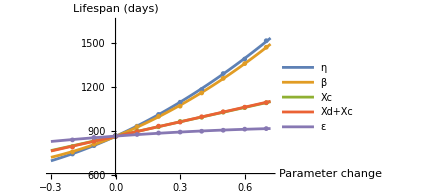
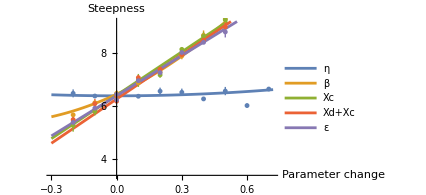
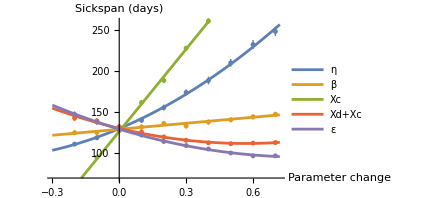
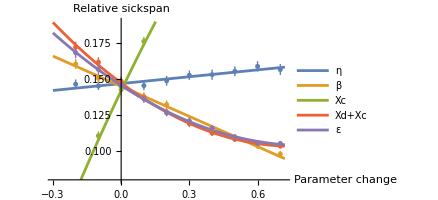

```mathematica
plotInfo={
{3,"Lifespan (days)",610,1650},
{4, "Steepness", 3.4,9.2},
{5,"Sickspan (days)",70,260},
{6,"Relative sickspan",0.08,0.19}
};
Grid[Table[{
Show[
Plot[Evaluate[polyModelsParChange[[j]]],{x,-.3,.72}
,PlotLegends->{"η", "β","Xc","Xd+Xc","ε"}
,PlotRange->{{-.3,.72},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{0,plotInfo[[j,3]]}
],
ListPlot[
Table[{#[[2]],#[[plotInfo[[j,1]]]]}&/@allSickspans[[i]],{i,{3,1,4,5,2}}]
,PlotRange->{{-.3,.72},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{0,plotInfo[[j,3]]}
],
AxesLabel->{"Parameter change",plotInfo[[j,2]]},
PlotRange->{{-.3,.72},{plotInfo[[j,3]],plotInfo[[j,4]]}},
AxesOrigin->{0,plotInfo[[j,3]]},
AxesStyle->Directive[Thickness@0.008,Black]
]}
,{j,Length@plotInfo}]]
```

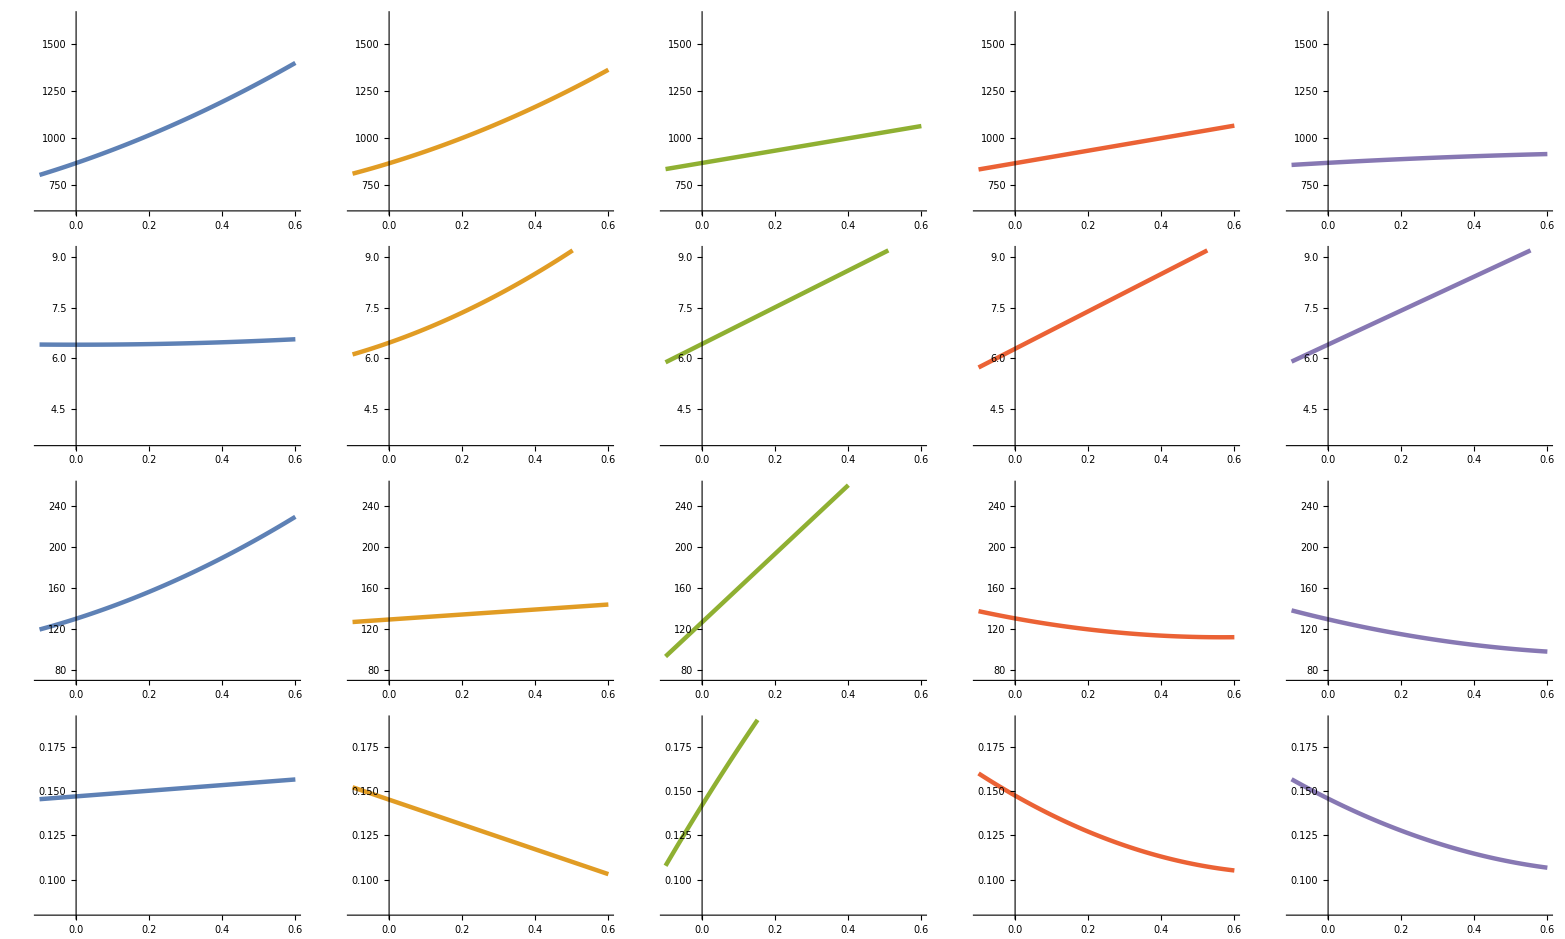

```mathematica
Grid[Table[Table[
Show[Plot[Evaluate[polyModelsParChange[[j,i]]],{x,-.1,.6}
(*,PlotLegends->{"Production rate η", "Removal rate β"}[[i]]*)
,PlotRange->{{-.1,.6},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,ImageSize->Tiny
,PlotStyle->Directive[Thickness@0.008,ColorData[97,"ColorList"][[i]]]
,AxesOrigin->{0,plotInfo[[j,3]]}
],
(*ListPlot[
{#[[2]],#[[plotInfo[[j,1]]]]}&/@allSickspans[[i]]
,PlotRange->{{-.1,.8},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{0,plotInfo[[j,3]]}
],*)
(*AxesLabel->{"Parameter change",plotInfo[[j,2]]},*)
PlotRange->{{-.1,.6},{plotInfo[[j,3]],plotInfo[[j,4]]}},
AxesOrigin->{0,plotInfo[[j,3]]},
AxesStyle->Directive[Thickness@0.006,Black]
],{i,5}]
,{j,Length@plotInfo}]]
```

```mathematica
polyModelsSteepnessLifespan:=
Table[(data={#[[3,1]]/866.3,#[[4,1]]/6.43}&/@allSickspans[[i]];
weights=(1./(#[[3,2]]*#[[4,2]]))&/@allSickspans[[i]];
fits=Table[Join[{j},{Length@j},LinearModelFit[data,j,vars,IncludeConstantBasis->False,Weights->weights][{"BestFit","AICc","BIC","AdjustedRSquared","RSquared"}]],{j,models}];
topByAICc=SortBy[fits,#[[4]]&][[1,3]]
),{i,{3,1,4,5,2}}];
polyModelsSteepnessLifespan//MatrixForm
```

(1.00075
0.0656405+0.940706 x
-1.26437+2.26243 x
0.995088 x^2
45.0248-94.5368 x+50.4989 x^2)

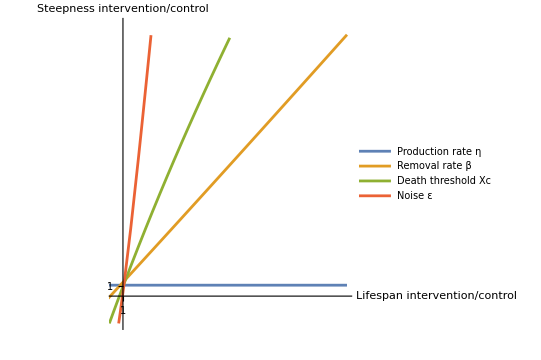

```mathematica
maxLifespan=Table[Max[#[[3,1]]+#[[3,2]]&/@allSickspans[[i]]]/863.5,{i,{3,1,4,2}}];
Show[LogLogPlot[Evaluate@MapThread[ConditionalExpression, {polyModelsSteepnessLifespan[[{1,2,3,5}]],And[x<#,x>825/863.5]&/@maxLifespan}],{x,.75,1.65}
,PlotLegends->{"Production rate η", "Removal rate β","Death threshold Xc","Noise ε"}
,PlotRange->{{.98,1.65},{.93,1.65}},
AxesOrigin->{1.,.98},
Axes->True
],
(*ListLogLogPlot[
Table[{#[[3]]/865.,#[[4]]/4.82}&/@allSickspans[[i]],{i,{3,1,4,2}}]
,PlotRange->{{.95,1.7},{.9,1.7}},
AxesOrigin->{1.,.95}
],*)
AxesLabel->{"Lifespan \n intervention/control","Steepness \n intervention/control"},
(*,PlotRange->{{825,1500},{4,8}},*)
AspectRatio->.9,
AxesStyle->Directive[Thickness@0.008,Black]
]
```

```mathematica
Mean@allSickspans[[;;,4,5]]
```

130.71.3

```mathematica
yfactors={130.,1.};
polyModelsLifespan:=Table[
Table[(data={#[[3,1]]/866.3,#[[j,1]]/yfactors[[j-4]]}&/@allSickspans[[i]];
weights=(1./(#[[3,2]]*#[[j,2]]))&/@allSickspans[[i]];
fits=Table[Join[{j},{Length@j},LinearModelFit[data,j,vars,IncludeConstantBasis->False,Weights->weights][{"BestFit","AICc","BIC","AdjustedRSquared","RSquared"}]],{j,models}];
topByAICc=SortBy[fits,#[[4]]&][[1,3]]
),{i,{3,1,4,5,2}}]
,{j,{5,6}}];
polyModelsLifespan//MatrixForm
```

(0.865162 x+0.139429 x^2 | 0.791092+0.202468 x | -5.74612+6.733 x | 4.95296-6.68619 x+2.7319 x^2 | 5.51176-4.51758 x
0.130824+0.0160095 x | 0.309688-0.22106 x+0.0569416 x^2 | -1.23667+1.91917 x-0.539249 x^2 | 0.923845-1.26325 x+0.485831 x^2 | 0.875344-0.729865 x)

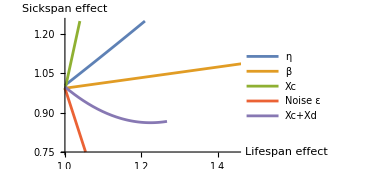
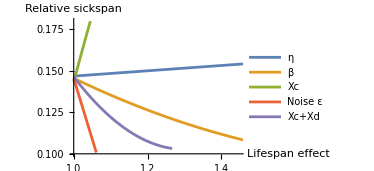

```mathematica
plotInfo={{5,"Sickspan effect",.75,1.25},{6,"Relative sickspan",0.1,0.18}};
maxLifespan=Table[Max[#[[3,1]]+#[[3,2]]&/@allSickspans[[i]]]/866.3,{i,{3,1,4,5,2}}];
order={1,2,3,5,4};
Grid[Table[{
Show[Plot[Evaluate@MapThread[ConditionalExpression, {polyModelsLifespan[[j]][[order]],And[x<#,x>0.8]&/@maxLifespan[[order]]}],{x,1.,1.6}
,PlotLegends->{"η", "β","Xc","Xc+Xd","Noise ε"}[[order]]
,PlotRange->{{1.,1.45},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{0,plotInfo[[j,3]]}
],
(*ListPlot[
Table[{#[[3]],#[[plotInfo[[j,1]]]]}&/@allSickspans[[i]],{i,{3,1,4,2}}]
,PlotRange->{{825,1200},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{825,1200,plotInfo[[j,3]]}
],*)
AxesLabel->{"Lifespan effect",plotInfo[[j,2]]},
PlotRange->{{1.,1.45},{plotInfo[[j,3]],plotInfo[[j,4]]}},
AxesOrigin->{1.,plotInfo[[j,3]]},
AxesStyle->Directive[Thickness@0.008,Black]
]}
,{j,Length@plotInfo}]]
```

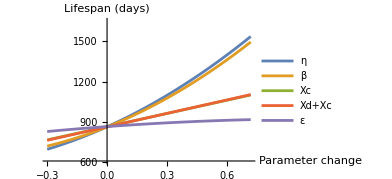
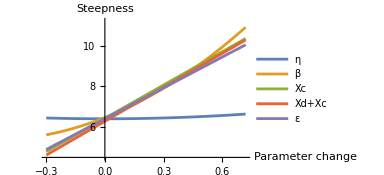
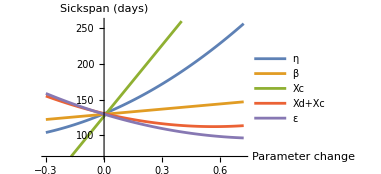
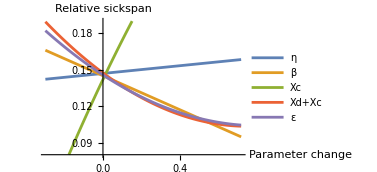

```mathematica
plotInfo={
{3,"Lifespan (days)",610,1650},
{4, "Steepness", 4.5,11.2},
{5,"Sickspan (days)",70,260},
{6,"Relative sickspan",0.08,0.19}
};
Grid[Table[{
Show[
Plot[Evaluate[polyModelsParChange[[j]]],{x,-.3,.72}
,PlotLegends->{"η", "β","Xc","Xd+Xc","ε"}
,PlotRange->{{-.3,.72},{plotInfo[[j,3]],plotInfo[[j,4]]}}
,AxesOrigin->{0,plotInfo[[j,3]]}
],
AxesLabel->{"Parameter change",plotInfo[[j,2]]},
PlotRange->{{-.3,.72},{plotInfo[[j,3]],plotInfo[[j,4]]}},
AxesOrigin->{0,plotInfo[[j,3]]},
AxesStyle->Directive[Thickness@0.008,Black]
]}
,{j,Length@plotInfo}]]
```